```mathematica
Tm=1356; (*melting temperature*)
dT=50; (* transition zone *)
dH=205000; (*latent heat*)
CpS=380; (*Heat capacity solid *)
(*CpL=530;*) (*Heat capacity liq*)
```

#### These are the values for the TiAl4V which are used in the modeling of the steady state :

```mathematica
Clear[CpL]
```

```mathematica
Tm=1877.15; (*melting temperature*)
Tl = 1923.15; (* liquidus *)
Tvl = 3563.15; (* liq. vapor *)
Tv = 3663.15;    (* vaporization *)
dT=10(Tl-Tm); (* transition zone *)
dH=2.86 10^11; (*latent heat*)
dV = 9.83*10^12; (* vaporization heat *)
dTv = 10(Tv-Tvl); (* transition vaporization *)


Clear[CpS]
CpS=ImportString["5.459e+08,300.129
5.73401e+08,428.341
6.04149e+08,556.591
6.28414e+08,670.555
6.52667e+08,798.729
6.83409e+08,934.084
7.07674e+08,1048.05
7.31927e+08,1176.22
6.88044e+08,1225.44
6.42538e+08,1274.63
6.66768e+08,1431.22
6.95869e+08,1587.87
7.23341e+08,1751.61
7.55673e+08,1929.61
7.99515e+08,1930.13
8.30362e+08,1937.6
8.49842e+08,1944.94
8.48051e+08,2150.95
8.47872e+08,2371.2
8.47716e+08,2563.03
8.45931e+08,2761.94
8.45764e+08,2967.98
8.45602e+08,3166.91
8.45487e+08,3309.01","Data"]; (*Heat capacity solid is a list*)
CpL = 8.45487 10^8;(*Heat capacity liq is a list*)
```

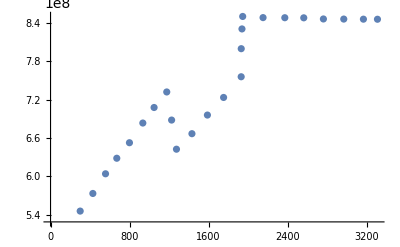

```mathematica
CpS[[All,{1,2}]] = CpS[[All,{2,1}]];
ListPlot[CpS]
```

```mathematica
CpL
```

8.45487×10^8

```mathematica
ufun=ListInterpolation[CpS[[All,2]],{{400,2400}}]
```

InterpolatingFunction[…]

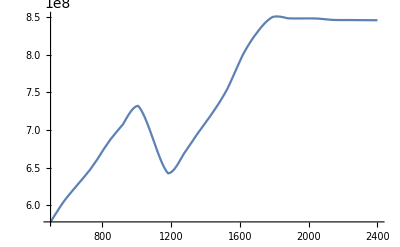

```mathematica
Plot[ufun[x],{x,500,2400}]
```

```mathematica
α[t_]:=1/2( 1+Tanh[4/dT*(t-Tm)]);
β[t_]:=1/2( 1+Tanh[4/dTv*(t-Tv)]);
dα[t_]=D[α[t],t]; dβ[t_]=D[β[t],t];
Cp[t_]:=ufun[t]*(1-α[t])+CpL*α[t]+dH*dα[t] + dV*dβ[t];
```

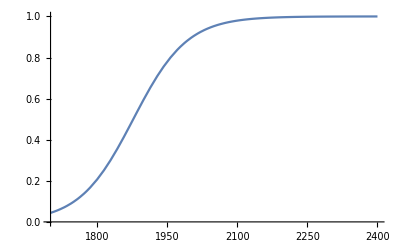

```mathematica
Plot[α[t],{t,1700,2400}]
```

```mathematica
N@Cp[1400]
```

7.09561×10^8

InterpolatingFunction::dmval: Input value {2999.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

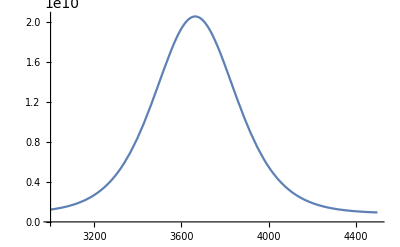

```mathematica
Plot[Cp[t],{t,2999,4500},PlotRange->Automatic]
```

```mathematica
CpL
```

530

```mathematica
TiAl4Vtable=Table[{N@Cp[t],t},{t,500,4500,30}]
```

InterpolatingFunction::dmval: Input value {2420} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2450} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2480} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{5.78044×10^8,500},{5.88821×10^8,530},{5.99412×10^8,560},{6.08934×10^8,590},{6.17406×10^8,620},{6.25514×10^8,650},{6.33524×10^8,680},{6.41702×10^8,710},{6.50315×10^8,740},{6.60405×10^8,770},{6.71163×10^8,800},{6.81768×10^8,830},{6.90827×10^8,860},{6.9916×10^8,890},{7.07211×10^8,920},{7.18858×10^8,950},{7.28118×10^8,980},{7.31607×10^8,1010},{7.20507×10^8,1040},{7.04148×10^8,1070},{6.85221×10^8,1100},{6.6631×10^8,1130},{6.50564×10^8,1160},{6.42832×10^8,1190},{6.48256×10^8,1220},{6.58677×10^8,1250},{6.70291×10^8,1280},{6.80357×10^8,1310},{6.90717×10^8,1340},{7.00827×10^8,1370},{7.10676×10^8,1400},{7.21067×10^8,1430},{7.32502×10^8,1460},{7.45648×10^8,1490},{7.61449×10^8,1520},{7.82384×10^8,1550},{8.09211×10^8,1580},{8.43267×10^8,1610},{8.8722×10^8,1640},{9.48776×10^8,1670},{1.03862×10^9,1700},{1.16986×10^9,1730},{1.35236×10^9,1760},{1.58343×10^9,1790},{1.82984×10^9,1820},{2.0247×10^9,1850},{2.0895×10^9,1880},{1.9937×10^9,1910},{1.78137×10^9,1940},{1.53435×10^9,1970},{1.31564×10^9,2000},{1.15018×10^9,2030},{1.03644×10^9,2060},{9.62708×10^8,2090},{9.16608×10^8,2120},{8.88422×10^8,2150},{8.7144×10^8,2180},{8.61328×10^8,2210},{8.55387×10^8,2240},{8.51976×10^8,2270},{8.50111×10^8,2300},{8.49211×10^8,2330},{8.48941×10^8,2360},{8.49119×10^8,2390},{8.49653×10^8,2420},{8.50515×10^8,2450},{8.5172×10^8,2480},{8.53316×10^8,2510},{8.55383×10^8,2540},{8.58033×10^8,2570},{8.61416×10^8,2600},{8.65722×10^8,2630},{8.71201×10^8,2660},{8.78165×10^8,2690},{8.87018×10^8,2720},{8.98266×10^8,2750},{9.12557×10^8,2780},{9.3071×10^8,2810},{9.53762×10^8,2840},{9.83029×10^8,2870},{1.02017×10^9,2900},{1.06729×10^9,2930},{1.12702×10^9,2960},{1.20268×10^9,2990},{1.29845×10^9,3020},{1.41951×10^9,3050},{1.57231×10^9,3080},{1.76481×10^9,3110},{2.00671×10^9,3140},{2.30975×10^9,3170},{2.68792×10^9,3200},{3.15747×10^9,3230},{3.73684×10^9,3260},{4.44606×10^9,3290},{5.30557×10^9,3320},{6.33417×10^9,3350},{7.54575×10^9,3380},{8.94469×10^9,3410},{1.052×10^10,3440},{1.2239×10^10,3470},{1.40411×10^10,3500},{1.58357×10^10,3530},{1.75048×10^10,3560},{1.89139×10^10,3590},{1.99312×10^10,3620},{2.04512×10^10,3650},{2.04164×10^10,3680},{1.98309×10^10,3710},{1.87588×10^10,3740},{1.73102×10^10,3770},{1.56186×10^10,3800},{1.38171×10^10,3830},{1.2021×10^10,3860},{1.03171×10^10,3890},{8.76222×10^9,3920},{7.38616×10^9,3950},{6.19763×10^9,3980},{5.19077×10^9,4010},{4.35087×10^9,4040},{3.65878×10^9,4070},{3.09401×10^9,4100},{2.63669×10^9,4130},{2.26862×10^9,4160},{1.97383×10^9,4190},{1.73861×10^9,4220},{1.5515×10^9,4250},{1.40301×10^9,4280},{1.28539×10^9,4310},{1.19236×10^9,4340},{1.11886×10^9,4370},{1.06085×10^9,4400},{1.0151×10^9,4430},{9.79031×10^8,4460},{9.50613×10^8,4490}}

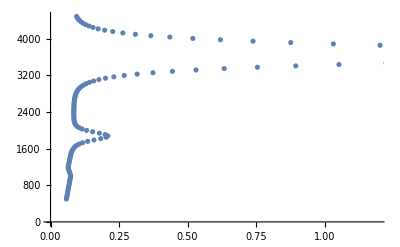

```mathematica
ListPlot[TiAl4Vtable]
```

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\TiAl4VValues.csv",TiAl4Vtable];
```

```mathematica
Clear[Tm,dT,dH,CpS,CpL];
Tm=1288; Ts=1188;
(*melting temperature*)
dT=50; (* transition zone *)
dH=60; (*latent heat*)
CpS=0.396; (*Heat capacity solid *)
CpL=0.49; (*Heat capacity liq*)
```

```mathematica
Plot[Cp[t],{t,1000,1250},PlotRange->{All,{0,7}},Frame->True]
```

-Graphics-

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\BronzeValues.csv",Table[{N@Cp[t]*10^9,t},{t,1150,1230,5}]]
```

C:\Users\tonii\OneDrive\Documents\GitHub\Mathematica\BronzeValues.csv

```mathematica
(*function used in abaqus to smooth transition from solid to liq*)
ζ[t_]:=(t-Ts)/(Tm-Ts)
Ut[θ_]:=(ζ[θ])^3(10-15 ζ[θ]+6 ζ[θ]^2)
dUt[θ_]=D[Ut[θ],θ]
```

(3 (10-3/20 (-1188+θ)+(3 (-1188+θ)^2)/5000) (-1188+θ)^2)/1000000+((-3/20+(3 (-1188+θ))/2500) (-1188+θ)^3)/1000000

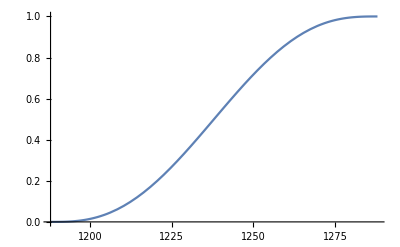

```mathematica
Plot[Ut[θ],{θ,1188,1288}]
```

```mathematica
Cp[t_]:=CpS(1-Ut[t])+CpL Ut[t]+dH dUt[t];
```

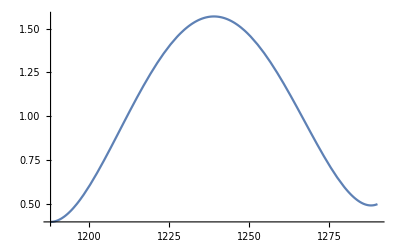

```mathematica
Plot[Cp[t],{t,1188,1290}]
```

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\BronzeValues.csv",Table[{N@Cp[t]*10^9,t},{t,1188,1288,5}]]
```

C:\Users\tonii\OneDrive\Documents\GitHub\Mathematica\BronzeValues.csv

```mathematica
Mean[{0.45,0.11,0.08}]
```

0.213333

```mathematica
Clear[Tm,dT,dH,CpS,CpL];
Tm=1; Ts=0.95; 
(*melting temperature*)
dT=0.1; (* transition zone *)
dH=1; (*latent heat*)
CpS=1; (*Heat capacity solid *)
CpL=1;
```

```mathematica
α[t_]:=1/2( 1+Tanh[4/dT*(t-Tm)]);
dα[t_]=D[α[t],t]
Cp[t_]:=CpS*(1-α[t])+CpL*α[t]+dH*dα[t];
```

20. Sech[40. (-1+t)]^2

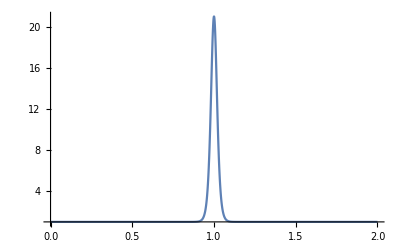

```mathematica
Plot[Cp[t],{t,0,2},PlotRange->All]
```

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\freezingsolid_appHeat.csv",Table[{N@Cp[t],t},{t,0,2,0.05}]]
```

C:\Users\tonii\OneDrive\Documents\GitHub\Mathematica\freezingsolid_appHeat.csv